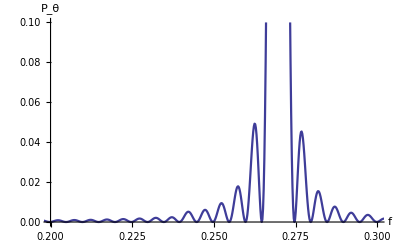

frequence/Hz | peak
0.073 | 0.0114164
0.0802 | 0.27357
0.0872 | 0.0147303
0.2574 | 0.0178747
0.2624 | 0.0492584
0.2696 | 1.
0.2768 | 0.045355
0.2818 | 0.0154566
0.4296 | 0.011493
0.6194 | 0.0839263

```mathematica
ps=Import["E:/data/thetaps.dat"];
len=Length[ps];p=Table[ps[[j,2]],{j,len}];
Emax=Max[p];
unitps=Table[{ps[[j,1]],ps[[j,2]]/Emax},{j,len}];
ListLinePlot[unitps,AxesLabel->{"f","P_θ"},PlotRange->{{0.2,0.3},{0,0.1}},BaseStyle->{FontSize->13},PlotStyle->Thickness[0.004],AxesStyle->Thickness[0.003]]
len=Length[unitps];ref=10^-2;
peak={{"frequence/Hz","peak"}};
ahead=unitps[[1,2]];middle=unitps[[2,2]];
If[ahead>middle,AppendTo[peak,unitps[[1]]]];
Do[If[(unitps[[j-2,2]]<unitps[[j-1,2]]>unitps[[j,2]])&&(middle>ref),AppendTo[peak,unitps[[j-1]]]];
ahead=unitps[[j-1,2]];middle=unitps[[j,2]],{j,3,len}]
peak//TableForm
Clear[ps,len,p,Emax,unitps,peak,ahead,middle,ref]
```